# Homework 3

#### Camila Lozano Sierra Wyllie

#### Problem 1: Connect-4

```mathematica
play[]:=
Module[
{listD,listR,listY,columnCount,count,horizR,horizY,vertR,vertY,diagRPos,diagRNeg,diagYPos,diagYNeg,cnt1,cnt2,cnt3,cnt4,countt,PosList,count4,listOfDiag,listOfDiagg},
columnCount={1,1,1,1,1,1,1};(*number of disks in each column*)
count=1;
listD={};(*list of disks*)
listR={};(*list of red *)
listY={};(*list of yellow*)
x=Input["Press any number to start, -1 to quit:"];
While[x≠-1,
draw=0;
For[f=1,f≤Length[columnCount],f++,
If[columnCount[[f]]==7,
draw+=1;
];
];
If[draw==7,
Print["Draw"];
Break[];
];

If [OddQ[count],x=Input["drop red disk at column (1-7):"],x=Input["drop yellow disk at column (1-7):"]];
If[OddQ[count]==True,AppendTo[listR,{x,columnCount[[x]]}],AppendTo[listY,{x,columnCount[[x]]}]];
(*adding coordinates to a list that corresponds to disk color*)
AppendTo[listD, {If[OddQ[count]==True,
{Red,Disk[{x,columnCount[[x]]},.5]},{Yellow,Disk[{x,columnCount[[x]]},.5]}]}];
(*list of disks for graphic purposes*)
count++;
columnCount[[x]]++;

Print[
Graphics[{listD,Table[Circle[{i,j},{.5,.5}],{i,1,7},{j,1,6}]},Frame->True]];

horizR=SortBy[listR, Last];horizY=SortBy[listY,Last];(*coordinates of disks are in chronological order*)

(*horizontal win by red*)
If[Length[horizR]≥4,
cnt1=0;
For[i=1,i<Length[horizR],i++,
If[horizR[[i,2]]==horizR[[i+1,2]]&& 
(horizR[[i,1]]+1)==horizR[[i+1,1]]
,cnt1++;,cnt1=0;];
If[cnt1==3,Return["Red Player Has Won"];]
];
];

(*horizontal win by yellow*)
If[Length[horizY]≥4,
cnt2=0;
For[i=1,i<Length[horizY],i++,
If[horizY[[i,2]]==horizY[[i+1,2]]&& 
(horizY[[i,1]]+1)==horizY[[i+1,1]]
,cnt2++;,cnt2=0;];
If[cnt2==3,Return["Yellow Player Has Won"];]
];
];

vertR=SortBy[listR,First];
vertY= SortBy[listY,First];

(*vertical win by red*)
If[Length[vertR]≥4,
cnt3=0;
For[i=1,i<Length[vertR],i++,
If[vertR[[i,1]]==vertR[[i+1,1]]&& 
(vertR[[i,2]]+1)==vertR[[i+1,2]]
,cnt3++;,cnt3=0];
If[cnt3==3,Return["Red Player Has Won"];]
];
];

(*vertical win by yellow*)
If[Length[vertY]≥4,
cnt4=0;
For[i=1,i<Length[vertY],i++,
If[vertY[[i,1]]==vertY[[i+1,1]]&& 
(vertY[[i,2]]+1)==vertY[[i+1,2]]
,cnt4++;,cnt4=0;];
If[cnt4==3,Return["Yellow Player Has Won"];]
];
];



(*diagonal win by red*)
diagRPos= Sort[listR];

(*diagonal win by yellow*)
diagYPos= Sort[listY];


If[Length[listR]==21 &&Length[listY]==21, Return["Draw"];];

If [OddQ[count],PosList=diagRPos,PosList=diagYPos];

listOfDiag  (*Positive List*)
 ={
{1,3},{2,4},{3,5},{4,6},
{1,2},{2,3},{3,4},{4,5},
{2,3},{3,4},{4,5},{5,6},
{1,1},{2,2},{3,3},{4,4},
{2,2},{3,3},{4,4},{5,5},
{3,3},{4,4},{5,5},{6,6},
{2,1},{3,2},{4,3},{5,4},
{3,2},{4,3},{5,4},{6,5},
{4,3},{5,4},{6,5},{7,6},
{3,1},{4,2},{5,3},{6,4},
{4,2},{5,3},{6,4},{7,5},
{4,1},{5,2},{6,3},{7,4}};

listOfDiagg (*Negative List*)
 ={
{7,3},{6,4},{5,5},{4,6},
{7,2},{6,3},{5,4},{4,5},
{6,3},{5,4},{4,5},{5,6},
{7,1},{6,2},{5,3},{4,4},
{6,2},{5,3},{4,4},{3,5},
{5,3},{4,4},{3,5},{2,6},
{6,1},{5,2},{4,3},{3,4},
{5,2},{4,3},{3,4},{2,5},
{4,3},{3,4},{2,5},{1,6},
{5,1},{4,2},{3,3},{2,4},
{4,2},{3,3},{2,4},{1,5},
{4,1},{3,2},{2,3},{1,4}};

If[Length[PosList]≥4,
count4=0;
For[i=1,i≤4,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiag[[i]],count4++];
];
If[count4==4,
If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
count4=0;
For[i=5,i≤8,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiag[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
count4=0;
For[i=9,i≤12,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiag[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
count4=0;
For[i=13,i≤16,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiag[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
count4=0;
For[i=17,i≤20,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiag[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
count4=0;
For[i=21,i≤24,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiag[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
count4=0;
For[i=25,i≤28,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiag[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
count4=0;
For[i=29,i≤32,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiag[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
count4=0;
For[i=33,i≤36,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiag[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
count4=0;
For[i=37,i≤40,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiag[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
count4=0;
For[i=41,i≤44,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiag[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
count4=0;
For[i=45,i≤48,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiag[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];

];


count4=0;
For[i=1,i≤4,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiagg[[i]],count4++];
];
If[count4==4,
If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];

count4=0;
For[i=5,i≤8,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiagg[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
count4=0;
For[i=9,i≤12,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiagg[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
count4=0;
For[i=13,i≤16,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiagg[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
count4=0;
For[i=17,i≤20,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiagg[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
count4=0;
For[i=21,i≤24,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiagg[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
count4=0;
For[i=25,i≤28,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiagg[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
count4=0;
For[i=29,i≤32,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiagg[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
count4=0;
For[i=33,i≤36,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiagg[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
count4=0;
For[i=37,i≤40,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiagg[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"];
];
];
];
count4=0;
For[i=41,i≤44,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiagg[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
count4=0;
For[i=45,i≤48,i++,
For[j=1,j≤Length[PosList],j++,
If[PosList[[j]]==listOfDiagg[[i]],count4++];
];
If[count4==4,If[OddQ[count],Return["Red Player Has Won"],Return["Yellow Player Has Won"]];
];
];
];
];


];
];
```

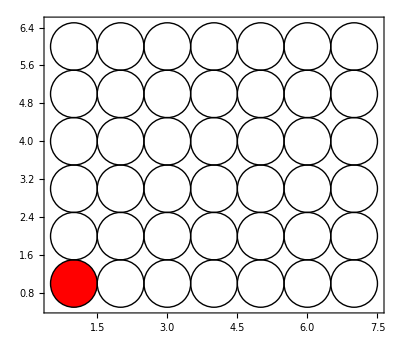

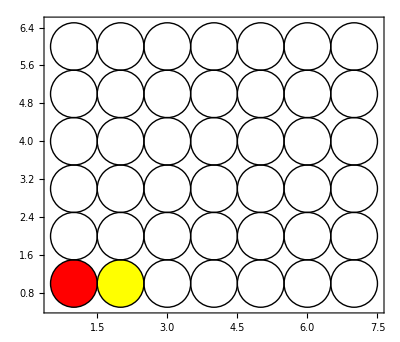

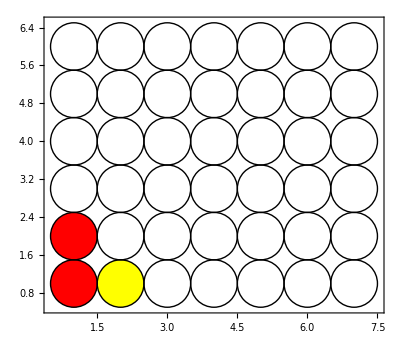

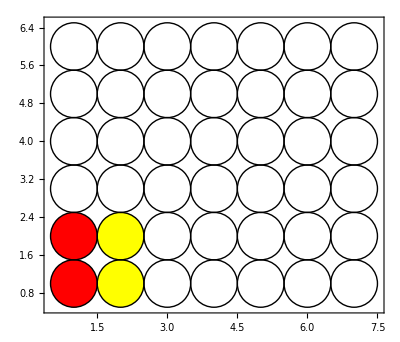

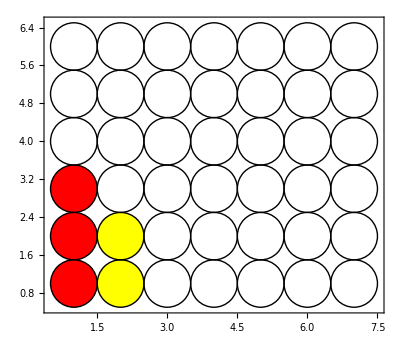

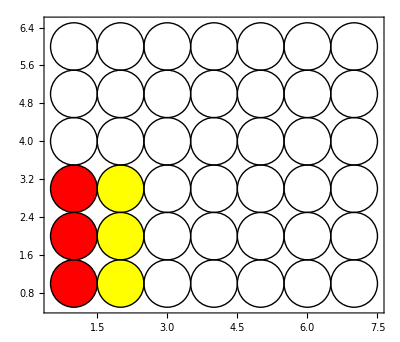

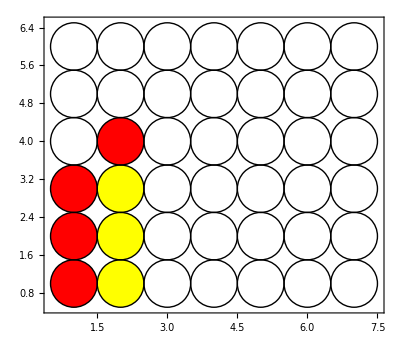

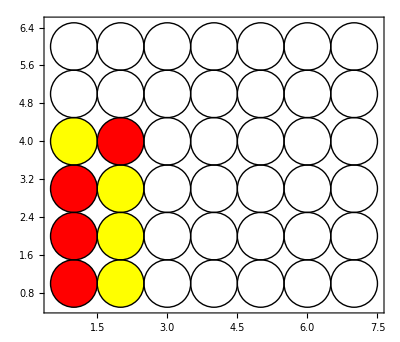

Draw

```mathematica
play[]
```

#### Problem 2 Animation on Locker Doors

```mathematica
haveFun[n_]:=
Module[
{total},
(*initializes doors*)
list =lockDoors[n];
(*our doors pics, slows things down a bit, but looks decent*)
image1=Import["https://www.kargomaster.com/pub/media/catalog/product/cache/c687aa7517cf01e65c009f6943c2b1e9/k/m/km-40220-cabinet-locker-full-door-rendering.jpg"];
image2=Import["https://banner2.kisspng.com/20180419/vyw/kisspng-locker-door-shelf-file-cabinets-empty-shelf-5ad89a1fef5d72.1764107715241446719805.jpg"];

(*running list for the animation*)
total = {list};

(*loop sequence to start passes*)
For[i=1,i≤n,i++,(*per pass*)
For[j=1,j≤n,j++,(*per door*)
If[Mod[j,i]==0,
list = toggle[list,j];
];
];
total=AppendTo[total,list];
];
Print[total];

(*make number to image replacement*)
total = Replace[total,{0:>{image1},1:>{image2}},All];
(*creates animation*)
Return[Animate[Grid[total[[i]], Frame->All],{i,1,Length@total,1}]];
]
```

```mathematica
toggle[l_,i_]:=
Module[
{idex=i,
list=l},
(*toggles door*)
If[list[[i]]==0,
list[[i]]=1,
list[[i]]=0];
Return[list]];
```

```mathematica
lockDoors[n_]:=
Module[
(*resets all the doors*)
{numDoors=n},
list=Table[0,numDoors];
list2=MatrixForm[list];
Return[list]];
```

```mathematica
haveFun[5]
```

{{0,0,0,0,0},{1,1,1,1,1},{1,0,1,0,1},{1,0,0,0,1},{1,0,0,1,1},{1,0,0,1,0}}

#### Problem 3:

```mathematica
equilateralTriangle[n_]:=
Module[
{triangle=n},
(*Generates triangle*)
triangle=Table[RandomInteger[{1,9}],{i,1,n},{j,i}];
Return[triangle];
]
```

```mathematica
triangleMinSum[n_]:=
Module[
{levels=n},
triangle=equilateralTriangle[levels];

deepest=triangle[[levels]];
listy=triangle;

(*loop thru triangle levels and each position on the row*)
(*initialization of l because we need to add the element to the one above it to determine sum*)
(*Bottom up implementation is faster since we can store the bottom layer sums as we go up the triangle*)
For[l=levels-1,l≥1,l--,
For[i=1,i≤l,i++,
(*choose smallest between two nodes, add to the node above, store this value *)
deepest[[i]]=Min[deepest[[i]],deepest[[i+1]]]+triangle[[l,i]];
];
listy[[l]]=deepest;
];

direction={};
over=1;

(*finds indexes of the path*)
For[i=2,i<=Length[listy],i++,
If[listy[[i,over]]<listy[[i,over+1]],
over=over;
direction=AppendTo[direction,over];
If[i==Length[listy],
direction=AppendTo[direction,over]],
direction=AppendTo[direction,over];
over=over+1;
If[i==Length[listy],
direction=AppendTo[direction,over]]];
];

(*creation of new triangle with coloured path*)
triangle2=triangle;
For[i=1,i≤Length[direction],i++,
triangle2[[i,direction[[i]]]]=Style[triangle2[[i,direction[[i]]]],Red];
];
(*Prints triangle*)
For[i=1,i≤n,i++,
triangle2[[i]]=Multicolumn[triangle2[[i]],i];
];
Print[Style[Column[triangle2,Center],Large]];

minSum=deepest[[1]];
Print["Minimum Sum: ",minSum];
];
```

```mathematica
triangleMinSum[5]
```

9
3 | 4
1 | 8 | 7
5 | 1 | 9 | 8
7 | 3 | 7 | 2 | 8

Minimum Sum: 17

```mathematica
triangleMinSum[1]
```

4

Minimum Sum: 4